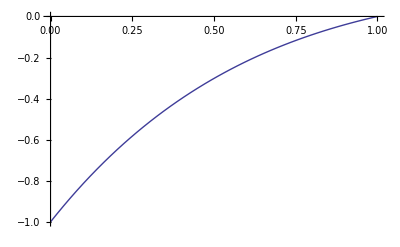

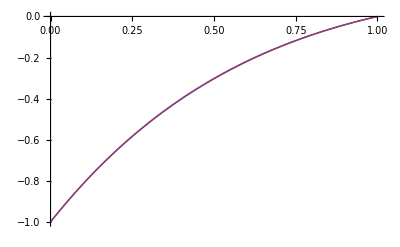

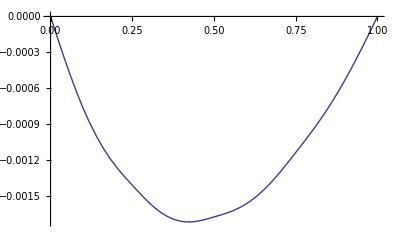

```mathematica
n=4;
delta=1/n;
x[0]=0;
x[n]=1;
Do[x[k]=k/n, {k, 1, n-1}];

fi[x_]:=-2*Exp[-x];

a=(6-(delta)^2)/(6*delta);
b =-(6+2*(delta)^2)/(3*delta);
c=(6-(delta)^2)/(6*delta);
(* {i, 1, n-1} покрива и горния ред, освен ако там не беше включила и а-то, което забравих да погледна изрично*)
Do[d[i]=(delta/6)*fi[(i-1)/n]+((2*delta)/3)*fi[i/n]+(delta/6)*fi[(i+1)/n], {i, 1, n-1}];
alfa[1]=-c/b;
beta[1]=(d[1]+a)/b;
(*според мен алфите не са ти равни*)
Do[{alfa[k]=-c/(alfa[k-1]a + b), beta[k] = (d[k] - a beta[k-1])/(alfa[k-1]a + b)},{k, 2, n - 1}];
(*beta[2]=d[2]/b;*)
(*Do[beta[i]=((Exp[(1-i)/n]*d[0])/b), {i, 2, n}];*)
(*beta[i]=((Exp[(1-i)/n]*d[0])/b);*)
y[0]=-1;
y[n]=0;

(*{i, n-1, 1,-1} за да циклиш на обратно*)
(*долу пишеше alfa[i];*y[i+1], но не съм сигурна дали ; не съм си я сложила аз без да искам. Случвало ми се е*)
Do[y[i]=alfa[i]*y[i+1]+beta[i], {i, n-1, 1,-1}];

Do[M[i]=y[i]+fi[i/n], {i, 0, n}];

(*на долния ред имаше грешно поставени скоби и един минус*)
P[i_, t_]:=-((t-x[i+1])^3*M[i])/(6*delta)+((t-x[i])^3*M[i+1])/(6*delta)+(t-x[i])*(delta*(M[i]-M[i+1])/6+(y[i+1]-y[i])/delta)+y[i]-(delta)^2*M[i]/6;
S[t_]:=Sum[If[t≥x[i]&& t≤x[i+1],P[i,t],0],{i,0,n-1}];

F[t_]:=(t-1)*Exp[-t];
Plot[S[t], {t,0,1},  PlotRange->All]
Plot[{F[t], S[t]}, {t, 0, 1}, PlotRange->All]
Plot[{F[t]-S[t]}, {t, 0, 1}]
```